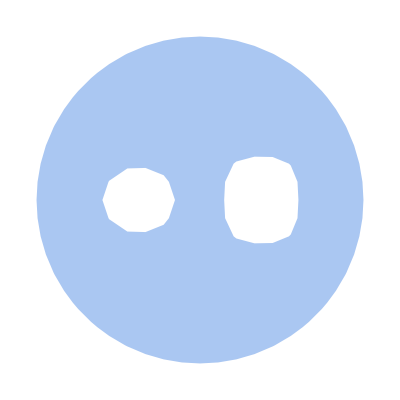

{DirichletCondition[u[x,y]==-5,0.8 Abs[-1.5+x]^3+0.5 Abs[y]^3==0.6],DirichletCondition[u[x,y]==5,Abs[1.5+x]^3+Abs[y]^1.5==0.7],DirichletCondition[u[x,y]==0,x^2+y^2==16]}

{{u→InterpolatingFunction[…]}}

-Graphics-

```mathematica
electrode1=x^2+y^2<=16; (*Внешний электрод*)
electrode2=0.8*Abs[-1.5+x]^3+0.5*Abs[y]^3<=0.6; (*Внутренний электрод 1*)
electrode3=Abs[1.5+x]^3+Abs[y]^1.5<=0.7; (*Внутренний электрод 2*)

(*Определение области для внешнего электрода*)
outerRegion=ImplicitRegion[electrode1,{x,y}];

(*Определение области для внутреннего электрода 1*)
innerRegion1=ImplicitRegion[electrode2,{x,y}];

(*Определение области для внутреннего электрода 2*)
innerRegion2=ImplicitRegion[electrode3,{x,y}];
(*Объединение областей*)
fullRegion=RegionDifference[RegionDifference[outerRegion,innerRegion1],innerRegion2];
Region[fullRegion]
laplaceEquation = Laplacian[u[x,y], {x,y}] == 0;
conditions = {
DirichletCondition[u[x,y]== -5, 0.8*Abs[-1.5+x]^3+0.5*Abs[y]^3==0.6],
DirichletCondition[u[x,y]== 5, Abs[1.5+x]^3+Abs[y]^1.5==0.7],
DirichletCondition[u[x,y]== 0, x^2+y^2 == 16]
}

sol = NDSolve[{laplaceEquation, conditions}, u, {x,y} ∈ fullRegion]
solPlot = ContourPlot[u[x,y]/. First[sol],{x,y}∈fullRegion,Contours->20,ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

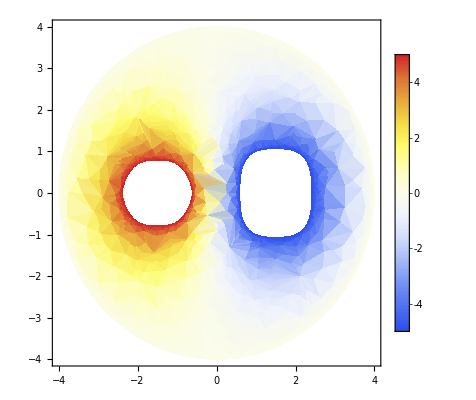

```mathematica
DensityPlot[u[x,y]/. First[sol],{x,y}∈fullRegion,ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

```mathematica
contourPlot = ContourPlot[Evaluate[u[x,y]/. sol]==1,{x,y}∈fullRegion,Contours->{1},PlotLegends->Automatic, ContourStyle->Black];
Show[solPlot, contourPlot]
```

-Graphics-

```mathematica
points=Cases[Normal@contourPlot,Line[pts_]:>pts,Infinity];
pointPairs=Flatten[points,1];
totalDistance = 0;
For[i=1,i<=Length[pointPairs]-1,i++,totalDistance+= EuclideanDistance[pointPairs[[i]], pointPairs[[i+1]]]]
totalDistance
```

12.7915